## Main Program

### Interface

#### Temporary Interface

```mathematica
interface[deltaT_,t_,r_,height_,dens_,fuel_,ρ0_,g0_,θ_,stages_]:=Module[{data={},v=0,h=0,mt=0,rocketpos={},rocketdisplay},
data=rocket[deltaT,t,r,height,dens,fuel,ρ0,g0];
v=data[[1]];
h=data[[2]];
mt=data[[3]];
rocketpos={0,0,h};
Switch[stages,
1,rocketdisplay=SSRocket[r,height,rocketpos,θ],
2,rocketdisplay=DSRocket[{}],
3,rocketdisplay=TSRocket[{}]
];
Row[{
rocketdisplay,
Column[{
Text[Style["Current Velocity: " <>ToString[v]<>" m/s",Large]],
Text[Style["Current Altitude: " <>ToString[h]<>" m",Large]],
Text[Style["Current Mass: " <>ToString[mt]<>" Kg",Large]]
}]
},ImageSize->800
]
]
```

```mathematica
Manipulate[interface[.1,t,r,h,d,fm,ρ,g,θ,1],
{{t,0,"Time"},0,1000},
{{r,5,"Radius"},3,12},
{{h,110,"Height"},50,200},
{{d,20,"Material Density"},10,50},
{{fm,2500000,"Fuel Mass"},1500000,3500000},
{{ρ,1,"Atmospheric Pressure at Sea Level"},0,1},
{{g,9.8,"Gravitational Acceleration"},0,9.8},
{{θ,0,"Angle"},-π/2,π/2}
]
```

#### Final Interface

```mathematica
PrimaryInterface=DynamicModule[{currentMenu=mainmenu,stages,stagedata={3,50,{0,0,0},14000},α1=14000,α2=5000,α3=1000,rocketdisplay,rocketfunction,rocket1r=5,rocket2r=5,rocket3r=3,rocket1h=50,rocket2h=30,rocket3h=40,rocketmenu,rocketmenumain,rocket1menu,rocket2menu,rocket3menu,stage1,stage2,stage3,evmenu,mainmenu,t=0,DeltaT=0.5,density=17,fuelmass=2500000,ρ=1.225,g0=9.8,Vg=2500,R=6371000,H=7000,LEO=500000,data={{0,0,0},0,0,0,0},rocketpos={0,0,0},θ=0,rocketstats={3,50,{0,0,0}}},
mainmenu=Dynamic@Column[{
stages,
Text[Style["Delta-T Interval (s)",Medium]],
Slider[Dynamic[DeltaT],{0.0001,5},Appearance->"Labeled"],
Text[Style["Current Time (s)",Medium]],
Slider[Dynamic[t],{0,1000},Appearance->"Labeled"],
Text[Style["Rocket Inclination (Radians)",Medium]],
Slider[Dynamic[θ],{-π/2,π/2},Appearance->"Labeled"],
Text[Style["Current Velocity: " <>ToString[AccountingForm[data[[3]]]]<>" m/s",Large]],
Text[Style["Current Altitude: " <>ToString[AccountingForm[data[[5]]]]<>" m",Large]],
Text[Style["Current Atmospheric Pressure: " <>ToString[ρ]<>" kg/m^3",Large]],
Text[Style["Current Gravitational Acceleration: " <>ToString[g0]<>" m/s",Large]],
Text[Style["Current Mass: " <>ToString[AccountingForm[data[[4]]]]<>" kg",Large]]
}];
rocketmenumain=Dynamic@Column[{
Dynamic[rocketmenu]
}];
rocket1menu=Dynamic@Column[{
rocketmenu=stage1;
rocketstats={Dynamic[rocket1r],Dynamic[rocket1h],data[[1]]};
rocketdisplay=SSRocket[rocketstats,Dynamic[θ]];
stagedata={Dynamic[rocket1r],Dynamic[rocket1h],data[[1]],Dynamic[α1]};
}];
stage1=Dynamic@Column[{
Text[Style["Rocket Radius (m)",Medium]],
Slider[Dynamic[rocket1r],{1,10},Appearance->"Labeled"],
Text[Style["Rocket Height (m)",Medium]],
Slider[Dynamic[rocket1h],{20,200},Appearance->"Labeled"],
Text[Style["Engine Thrust (kN)",Medium]],
Slider[Dynamic[α1],{10000,50000},Appearance->"Labeled"]
}];
rocket2menu=Dynamic@Column[{
rocketmenu=stage2;
rocketstats={{Dynamic[rocket1r],Dynamic[rocket1h],data[[1,1]]},{Dynamic[rocket2r],Dynamic[rocket2h],data[[1,2]]}};
rocketdisplay=DSRocket[rocketstats,Dynamic[θ]];
stagedata={{Dynamic[rocket1r],Dynamic[rocket1h],data[[1,1]],Dynamic[α1]},{Dynamic[rocket2r],Dynamic[rocket2h],data[[1,2]],Dynamic[α2]}};
}];
stage2=Dynamic@Column[{
Text[Style["Stage 1 Radius (m)",Medium]],
Slider[Dynamic[rocket1r],{1,10},Appearance->"Labeled"],
Text[Style["Stage 1 Height (m)",Medium]],
Slider[Dynamic[rocket1h],{20,100},Appearance->"Labeled"],
Text[Style["Engine 1 Thrust (kN)",Medium]],
Slider[Dynamic[α1],{10000,50000},Appearance->"Labeled"],
Text[Style["Stage 2 Radius (m)",Medium]],
Slider[Dynamic[rocket2r],{1,10},Appearance->"Labeled"],
Text[Style["Stage 2 Height (m)",Medium]],
Slider[Dynamic[rocket2h],{20,100},Appearance->"Labeled"],
Text[Style["Engine 2 Thrust (kN)",Medium]],
Slider[Dynamic[α2],{1000,10000},Appearance->"Labeled"]
}];
rocket3menu=Dynamic@Column[{
rocketmenu=stage3;
rocketstats={{Dynamic[rocket1r],Dynamic[rocket1h],data[[1,1]]},{Dynamic[rocket2r],Dynamic[rocket2h],data[[1,2]]},{Dynamic[rocket3r],Dynamic[rocket3h],data[[1,3]]}};
rocketdisplay=TSRocket[rocketstats,Dynamic[θ]];
stagedata={{Dynamic[rocket1r],Dynamic[rocket1h],data[[1,1]],Dynamic[α1]},{Dynamic[rocket2r],Dynamic[rocket2h],data[[1,2]],Dynamic[α2]},{Dynamic[rocket3r],Dynamic[rocket3h],data[[1,3]],Dynamic[α3]}};
}];
stage3=Dynamic@Column[{
Text[Style["Stage 1 Radius (m)",Medium]],
Slider[Dynamic[rocket1r],{1,10},Appearance->"Labeled"],
Text[Style["Stage 1 Height (m)",Medium]],
Slider[Dynamic[rocket1h],{20,100},Appearance->"Labeled"],
Text[Style["Engine 1 Thrust (kN)",Medium]],
Slider[Dynamic[α1],{10000,50000},Appearance->"Labeled"],
Text[Style["Stage 2 Radius (m)",Medium]],
Slider[Dynamic[rocket2r],{1,10},Appearance->"Labeled"],
Text[Style["Stage 2 Height (m)",Medium]],
Slider[Dynamic[rocket2h],{20,100},Appearance->"Labeled"],
Text[Style["Engine 2 Thrust (kN)",Medium]],
Slider[Dynamic[α2],{1000,10000},Appearance->"Labeled"],
Text[Style["Stage 3 Radius (m)",Medium]],
Slider[Dynamic[rocket3r],{1,10},Appearance->"Labeled"],
Text[Style["Stage 3 Height (m)",Medium]],
Slider[Dynamic[rocket3h],{20,50},Appearance->"Labeled"],
Text[Style["Engine 3 Thrust (kN)",Medium]],
Slider[Dynamic[α3],{100,1000},Appearance->"Labeled"]
}];
evmenu=Dynamic@Column[{
Text[Style["Atmospheric Pressure (kg/m^3)",Medium]],
Slider[Dynamic[ρ],{0,10},Appearance->"Labeled"],
Text[Style["Gravitational Acceleration (m/s)",Medium]],
Slider[Dynamic[g0],{-10,20},Appearance->"Labeled"]
}];

Dynamic@Row[{

Dynamic[rocketdisplay],
Dynamic@Column[{
PopupMenu[Dynamic[stages],{rocket1menu->"1 Stage Rocket",rocket2menu->"2 Stage Rocket",rocket3menu->"3 Stage Rocket"}],
PopupMenu[Dynamic[currentMenu],{mainmenu->"Main Menu",rocketmenumain->"Rocket Menu",evmenu->"Planet Menu"}],
(*
data=rocket[FinishDynamic[];DeltaT,t,rocket1r,rocket1h,density,fuelmass,ρ,g0];
rocketpos=data[[4]];
*)
data=stages[FinishDynamic[];stagedata,t,density,fuelmass,ρ,Vg,R,H,LEO];

Dynamic[currentMenu]
},Frame->True]

},ImageSize->900,Frame->True]
]
```

### Animation Resources

#### Single Stage Rocket

```mathematica
SSRocket[stage_,θ_]:=Module[{noseconebasepos={0,0,0},noseconetoppos={0,0,0},stage1bottom={0,0,0},engine1bottom={0,0,0},engine1top={0,0,0},groundpos={},launchpad={},i,flame1point={0,0,0},flamelength=0,stage1pos={}},

(* Sets the positions of each of the stages and checks to see if they are clipping into the launchpad *)
stage1pos=stage[[3]];
If[stage1pos[[3]]<10,stage1pos[[3]]=10];

(* Creates the ground and launchpad *)
groundpos={{-stage[[1]]*5,-stage[[1]]*5,0},{-stage[[1]]*5,stage[[1]]*5,0},{stage[[1]]*5,stage[[1]]*5,0},{stage[[1]]*5,-stage[[1]]*5,0}};
launchpad=Table[{groundpos[[i,1]]/1.5,groundpos[[i,2]]/1.5,groundpos[[i,3]]},{i,1,4}];
launchpad=Join[launchpad,Table[{launchpad[[i,1]],launchpad[[i,2]],launchpad[[i,3]]+10},{i,1,4}]];

(* Defines the nosecone as 1/8th the overall height of the rocket *)
noseconebasepos[[3]]=stage1pos[[3]]+(stage[[2]]-(stage[[2]]/8));
noseconetoppos[[3]]=stage1pos[[3]]+stage[[2]];

stage1bottom[[3]]=stage1pos[[3]]+(stage[[2]]/16);
engine1bottom[[3]]=stage1pos[[3]];
engine1top[[3]]=stage1pos[[3]]+(stage[[2]]/8);

(* Checks to see if the rocket is too close to the pad for the flame to display properly and if so, sets the flame length to the distance between the engine and the pad *)
If[4*(engine1top[[3]]-engine1bottom[[3]])<=engine1bottom[[3]]-launchpad[[5,3]],flamelength=4*(engine1top[[3]]-engine1bottom[[3]]),flamelength=engine1bottom[[3]]-launchpad[[5,3]]];
flame1point[[3]]=engine1bottom[[3]]-flamelength;

Graphics3D[{
Green,Polygon[groundpos],
Gray,Hexahedron[launchpad],
Rotate[{
Orange,Opacity[0.4],Cone[{engine1bottom,flame1point},stage[[1]]/1.5],Opacity[1],
FaceForm[RGBColor["#BCC6CC"]],Specularity[Gray,60],
Cone[{noseconebasepos,noseconetoppos},stage[[1]]],
Cylinder[{stage1bottom,noseconebasepos},stage[[1]]],
Cone[{engine1bottom,engine1top},stage[[1]]/1.5]},θ,{0,1,0},stage1pos]
},ImageSize->Medium,Boxed->False]
]
```

```mathematica
Manipulate[SSRocket[{5,100,{0,0,h}},θ],{h,0,500},{θ,-π/2,π/2}]
```

#### Two Stage Rocket

```mathematica
DSRocket[stages_,θ_]:=Module[{noseconebasepos={0,0,0},noseconetoppos={0,0,0},stage2bottom={0,0,0},stageskirtbottom={0,0,0},stageskirttop={0,0,0},stage1bottom={0,0,0},engine1bottom={0,0,0},engine1top={0,0,0},engine2bottom={0,0,0},engine2top={0,0,0},groundpos={},launchpad={},i,flame1point={0,0,0},flamelength=0,flame2point={0,0,0},stage1pos={},stage2pos={},height=stages[[1,2]]+stages[[2,2]]},

(* Sets the positions of each of the stages and checks to see if they are clipping into the launchpad *)
stage1pos=stages[[1,3]];
stage2pos=stages[[2,3]];
If[stage1pos[[3]]<10,stage1pos[[3]]=10];
If[stage2pos[[3]]<10,stage2pos[[3]]=10];

(* Creates the ground and launchpad *)
groundpos={{-stages[[1,1]]*5,-stages[[1,1]]*5,0},{-stages[[1,1]]*5,stages[[1,1]]*5,0},{stages[[1,1]]*5,stages[[1,1]]*5,0},{stages[[1,1]]*5,-stages[[1,1]]*5,0}};
launchpad=Table[{groundpos[[i,1]]/1.5,groundpos[[i,2]]/1.5,groundpos[[i,3]]},{i,1,4}];
launchpad=Join[launchpad,Table[{launchpad[[i,1]],launchpad[[i,2]],launchpad[[i,3]]+10},{i,1,4}]];

(* Defines the nosecone as 1/8th the overall height of the rocket *)
noseconebasepos[[3]]=stage2pos[[3]]+(height-(height/8));
noseconetoppos[[3]]=stage2pos[[3]]+height;
(* Defines the bottom of stage two as the height of the first stage plus the height of the engine *)
stage2bottom[[3]]=stage2pos[[3]]+stages[[1,2]]+(stages[[2,2]]/16);
(* Defines the height of the engine as 1/8 the height of the second stage, but only half of this will be showing (The fuselage hides the top of the cone) *)
engine2top[[3]]=stage2pos[[3]]+stages[[1,2]]+(stages[[2,2]]/8);
engine2bottom[[3]]=stage2pos[[3]]+stages[[1,2]];
(* Defines the skirt between the two stages such that it covers the second stage engine *)
stageskirtbottom[[3]]=stage1pos[[3]]+stages[[1,2]];
stageskirttop[[3]]=stage1pos[[3]]+stages[[1,2]]+(stages[[2,2]]/6);
(* Defines the engine of the rocket similarly to the second stage *)
stage1bottom[[3]]=stage1pos[[3]]+(stages[[1,2]]/16);
engine1bottom[[3]]=stage1pos[[3]];
engine1top[[3]]=stage1pos[[3]]+(stages[[1,2]]/8);
(* Since the second stage will always be covered unless it has separated, the flame can be defined simply as a cone that is 4 times the length of the engine *)
flame2point[[3]]=engine2bottom[[3]]-4*(engine2top[[3]]-engine2bottom[[3]]);

(* Checks to see if the rocket is too close to the pad for the flame to display properly and if so, sets the flame length to the distance between the engine and the pad *)
If[4*(engine1top[[3]]-engine1bottom[[3]])<=engine1bottom[[3]]-launchpad[[5,3]],flamelength=4*(engine1top[[3]]-engine1bottom[[3]]),flamelength=engine1bottom[[3]]-launchpad[[5,3]]];
If[stage1pos[[3]]≠stage2pos[[3]],flame1point[[3]]=engine1bottom[[3]],
flame1point[[3]]=engine1bottom[[3]]-flamelength];

Graphics3D[{
Green,Polygon[groundpos],
Gray,Hexahedron[launchpad],
Rotate[{
Orange,Opacity[0.4],Cone[{engine1bottom,flame1point},stages[[1,1]]/1.5],
Cone[{engine2bottom,flame2point},stages[[2,1]]/1.5],
Opacity[1],
FaceForm[RGBColor["#BCC6CC"]],Specularity[Gray,60],
Cone[{noseconebasepos,noseconetoppos},stages[[2,1]]],
Tube[{stageskirtbottom,stageskirttop},{stages[[1,1]],stages[[2,1]]}],
Cone[{engine2bottom,engine2top},stages[[2,1]]/1.5],
Cylinder[{stage2bottom,noseconebasepos},stages[[2,1]]],
Cylinder[{stage1bottom,stageskirtbottom},stages[[1,1]]],
Cone[{engine1bottom,engine1top},stages[[1,1]]/1.5]},θ,{0,1,0},stage2pos]
},ImageSize->Medium,Boxed->False]
]
```

```mathematica
Manipulate[DSRocket[{{5,50,{0,0,h}},{3,40,{0,0,h}}},θ],{h,0,500},{θ,-π/2,π/2}]
```

#### Three Stage Rocket

```mathematica
TSRocket[stages_,θ_]:=
Module[{noseconebasepos={0,0,0},noseconetoppos={0,0,0},stage2bottom={0,0,0},interstagebot={0,0,0},interstagetop={0,0,0},stageskirtbottom={0,0,0},stageskirttop={0,0,0},stage1bottom={0,0,0},engine1bottom={0,0,0},engine1top={0,0,0},engine2bottom={0,0,0},engine2top={0,0,0},stage3bottom={0,0,0},engine3bottom={0,0,0},engine3top={0,0,0},groundpos={},launchpad={},i,flame1point={0,0,0},flamelength=0,flame2point={0,0,0},flame3point={0,0,0},stage1pos={},stage2pos={},stage3pos={},height=stages[[1,2]]+stages[[2,2]]+stages[[3,2]]},

(* Sets the positions of each of the stages and checks to see if they are clipping into the launchpad *)
stage1pos=stages[[1,3]];
stage2pos=stages[[2,3]];
stage3pos=stages[[3,3]];
If[stage1pos[[3]]<10,stage1pos[[3]]=10];
If[stage2pos[[3]]<10,stage2pos[[3]]=10];
If[stage3pos[[3]]<10,stage3pos[[3]]=10];

(* Creates the ground and launchpad *)
groundpos={{-stages[[1,1]]*5,-stages[[1,1]]*5,0},{-stages[[1,1]]*5,stages[[1,1]]*5,0},{stages[[1,1]]*5,stages[[1,1]]*5,0},{stages[[1,1]]*5,-stages[[1,1]]*5,0}};
launchpad=Table[{groundpos[[i,1]]/1.5,groundpos[[i,2]]/1.5,groundpos[[i,3]]},{i,1,4}];
launchpad=Join[launchpad,Table[{launchpad[[i,1]],launchpad[[i,2]],launchpad[[i,3]]+10},{i,1,4}]];

(* Defines the nosecone as 1/8th the overall height of the rocket *)
noseconebasepos[[3]]=stage3pos[[3]]+(height-(height/8));
noseconetoppos[[3]]=stage3pos[[3]]+height;
(* Defines the bottom of stage two as the height of the first stage plus the height of the engine *)
stage3bottom[[3]]=stage3pos[[3]]+stages[[1,2]]+stages[[2,2]]+(stages[[3,2]]/16);
(* Defines the height of the engine as 1/8 the height of the second stage, but only half of this will be showing (The fuselage hides the top of the cone) *)
engine3top[[3]]=stage3pos[[3]]+stages[[1,2]]+stages[[2,2]]+(stages[[3,2]]/8);
engine3bottom[[3]]=stage3pos[[3]]+stages[[1,2]]+stages[[2,2]];
(* Defines the skirt between the two stages such that it covers the second stage engine *)
stageskirtbottom[[3]]=stage2pos[[3]]+stages[[1,2]]+stages[[2,2]];
stageskirttop[[3]]=stage2pos[[3]]+stages[[1,2]]+stages[[2,2]]+(stages[[3,2]]/6);
(* Defines the engine of the rocket similarly to the second stage *)
stage3bottom[[3]]=stage3pos[[3]]+stages[[1,2]]+stages[[2,2]]+(stages[[3,2]]/16);
(* Defines the height of the engine as 1/8 the height of the second stage, but only half of this will be showing (The fuselage hides the top of the cone) *)
engine2top[[3]]=stage2pos[[3]]+stages[[1,2]]+(stages[[2,2]]/8);
engine2bottom[[3]]=stage2pos[[3]]+stages[[1,2]];
stage2bottom[[3]]=stage2pos[[3]]+stages[[1,2]]+(stages[[2,2]]/16);
(* 1st-2nd interstage *)
interstagetop[[3]]=stage1pos[[3]]+stages[[1,2]]+(stages[[2,2]]/16);
interstagebot[[3]]=stage1pos[[3]]+stages[[1,2]];
stage1bottom[[3]]=stage1pos[[3]]+(stages[[1,2]]/16);
engine1bottom[[3]]=stage1pos[[3]];
engine1top[[3]]=stage1pos[[3]]+(stages[[1,2]]/8);
(* Since the second stage will always be covered unless it has separated, the flame can be defined simply as a cone that is 4 times the length of the engine *)
flame2point[[3]]=engine2bottom[[3]]-4*(engine2top[[3]]-engine2bottom[[3]]);
flame3point[[3]]=engine3bottom[[3]]-4*(engine3top[[3]]-engine3bottom[[3]]);

(* Checks to see if the rocket is too close to the pad for the flame to display properly and if so, sets the flame length to the distance between the engine and the pad *)
If[4*(engine1top[[3]]-engine1bottom[[3]])<=engine1bottom[[3]]-launchpad[[5,3]],flamelength=4*(engine1top[[3]]-engine1bottom[[3]]),flamelength=engine1bottom[[3]]-launchpad[[5,3]]];
If[stage1pos[[3]]≠stage2pos[[3]],flame1point[[3]]=engine1bottom[[3]],
flame1point[[3]]=engine1bottom[[3]]-flamelength];

Graphics3D[{
Green,Polygon[groundpos],
Gray,Hexahedron[launchpad],
Rotate[{
Orange,Opacity[0.4],Cone[{engine1bottom,flame1point},stages[[1,1]]/1.5],
Cone[{engine2bottom,flame2point},stages[[2,1]]/1.5],Cone[{engine3bottom,flame3point},stages[[3,1]]/1.5],
Opacity[1],
FaceForm[RGBColor["#BCC6CC"]],Specularity[Gray,60],
Cone[{noseconebasepos,noseconetoppos},stages[[3,1]]],
Cone[{engine3bottom,engine3top},stages[[3,1]]/1.5],
Cylinder[{stage3bottom,noseconebasepos},stages[[3,1]]],
Tube[{stageskirtbottom,stageskirttop},{stages[[2,1]],stages[[3,1]]}],
Cone[{engine2bottom,engine2top},stages[[2,1]]/1.5],
Cylinder[{stage2bottom,stageskirtbottom},stages[[2,1]]],
Cylinder[{interstagebot,interstagetop},stages[[1,1]]],
Cylinder[{stage1bottom,interstagebot},stages[[1,1]]],
Cone[{engine1bottom,engine1top},stages[[1,1]]/1.5]},θ,{0,1,0},stage3pos]
},ImageSize->Medium,Boxed->False]
]
```

```mathematica
Manipulate[TSRocket[{{5,50,{0,0,h}},{5,30,{0,0,h}},{3,40,{0,0,h}}},θ],{h,0,500},{θ,-π/2,π/2}]
```

### New Rocket Calculations

```mathematica
theta[t_,LEO_]:=π/2-ArcTan[(-1/t^2+LEO)/t]
```

Rocket Live new:

```mathematica
rocket[deltaT_,t_,r_,height_,dens_,fuel_,ρ0_,g0_,Vg_,R_,α_,H_,LEO_,v_,h_]:=
Module[{area=r^2*Pi,v1=0,v2=0,Tcurrent=deltaT,DeltaV=0,DeltaV1=0,DeltaV2=0,mt=r^2*height*dens+fuel,m0,TotalDV=0,values={},fuelcheck=True,d=0,θ=0},
m0=mt;
For[Tcurrent,Tcurrent≤t,Tcurrent+=deltaT,
DeltaV1=(Vg*α-mt*g0*(R/(R+h))^2-ρ0*area*ⅇ^(-h/H)*v^2)/mt*deltaT*Cos[theta[t,LEO]];
DeltaV2=(Vg*α-mt*g0*(R/(R+h))^2-ρ0*area*ⅇ^(-h/H)*v^2)/mt*deltaT*Sin[theta[t,LEO]];
DeltaV=√(DeltaV1^2+DeltaV2^2);
v+=DeltaV;
v1+=DeltaV1;
h+=v1*deltaT;
v2+=DeltaV2;
d+=v2*deltaT;
θ=theta[t,LEO]
];
Return[{v,h,d,mt,θ}]
]
```

```mathematica
Manipulate[rocket[.1,t,r,h,d,fm,ρ,g,2500,6371000,14000,7000,500000,0,0],
{t,0,500},
{r,3,10},
{h,50,200},
{d,10,50},
{fm,1500000,3500000},
{ρ,0,1},
{g,0,9.8}
]
```

AddTo::rvalue: 0 is not a variable with a value, so its value cannot be changed.

General::stop: Further output of AddTo :: rvalue will be suppressed during this calculation.

### Staging

```mathematica
stages[stage_,t_,dens_,fuel_,p0_,g0_,Vg_,R_,H_,LEO_]:=
Module[{h=0,length=Length[stage],values,staging=stage,v1=0,v2=0,v3=0,fT1=0,fT2=0,fT3=0,V1=0,V2=0,V3=0,h1=0,h2=0,h3=0},

If[length==4,

v1=stage⟦1⟧^2 π stage⟦2⟧;
fT1=v1/staging⟦4⟧;

While[t≤fT1,

values=rocket[.1,t,v1,stage⟦1⟧,dens,fuel,p0,g0,Vg,R,stage⟦4⟧,H,LEO,V1,h1];
V1=values⟦1⟧;
h1=values⟦2⟧;

Return[{{values⟦3⟧,0,values⟦2⟧},values⟦5⟧,values⟦1⟧,values⟦4⟧,values[[2]]}]
];

values=rocket[.1,t,v1,stage⟦1⟧,dens,0,p0,g0,Vg,R,0,H,LEO,V1,h1];
Return[{{values⟦3⟧,0,values⟦2⟧},values⟦5⟧,values⟦1⟧,values⟦4⟧,values[[2]]}],

If[length==2,

v1=stage⟦1,1⟧^2 π stage⟦1,2⟧;
v2=stage⟦1,1⟧^2 π stage⟦1,2⟧+stage⟦2,1⟧^2 π stage⟦2,2⟧;

fT1=v1/staging⟦1,4⟧;
fT2=v2/staging⟦2,4⟧;

While[t≤fT1,

values=rocket[.1,t,v2,stage⟦1,1⟧,dens,fuel,p0,g0,Vg,R,stage⟦1,4⟧,H,LEO,V1,h1];
staging⟦1,3,3⟧=values⟦2⟧;
staging⟦1,3,1⟧=values⟦3⟧;
staging⟦2,3,3⟧=values⟦2⟧;
staging⟦2,3,1⟧=values⟦3⟧;

V1=V2=values⟦1⟧;
h1=h2=values⟦2⟧;
Return[{{{staging⟦1,3,1⟧,0,staging⟦1,3,3⟧},{staging⟦2,3,1⟧,0,staging⟦2,3,3⟧}},values⟦5⟧,values⟦1⟧,values⟦4⟧,values[[2]]}]
];

While[t≤fT2,
v2=v2-v1;
values=rocket[.1,t,v1,stage⟦1,1⟧,dens,0,p0,g0,Vg,R,0,H,LEO,V1,h1]⟦2⟧;
staging⟦1,3,3⟧=values⟦2⟧;
h1=staging⟦1,3,1⟧=values⟦3⟧;
V1=values⟦1⟧;

values=rocket[.1,t,v2,stage⟦2,1⟧,dens,fuel,p0,g0,Vg,R,stage⟦2,4⟧,H,LEO,V2,h2];
staging⟦2,3,3⟧=values⟦2⟧;
staging⟦2,3,1⟧=values⟦3⟧;
V2=values⟦1⟧;
h2=values⟦2⟧;
Return[{{{staging⟦1,3,1⟧,0,staging⟦1,3,3⟧},{staging⟦2,3,1⟧,0,staging⟦2,3,3⟧}},values⟦5⟧,values⟦1⟧,values⟦4⟧,h2}]
];

values=rocket[.1,t,v1,stage⟦1,1⟧,dens,0,p0,g0,Vg,R,0,H,LEO,V1,h1];
staging⟦1,3,3⟧=values⟦2⟧;
staging⟦1,3,1⟧=values⟦3⟧;

values=rocket[.1,t,v1,stage⟦1,1⟧,dens,0,p0,g0,Vg,R,0,H,LEO,V2,h2];
staging⟦2,3,3⟧=values⟦2⟧;
staging⟦2,3,1⟧=values⟦3⟧;
Return[{{{staging⟦1,3,1⟧,0,staging⟦1,3,3⟧},{staging⟦2,3,1⟧,0staging⟦2,3,3⟧}},values⟦5⟧,values⟦1⟧,values⟦4⟧,values[[2]]}],

v1=stage⟦1,1⟧^2 π stage⟦1,2⟧;
v2=stage⟦1,1⟧^2 π stage⟦1,2⟧+stage⟦2,1⟧^2 π stage⟦2,2⟧;
v3=stage⟦1,1⟧^2 π stage⟦1,2⟧+stage⟦2,1⟧^2 π stage⟦2,2⟧+stage⟦3,1⟧^2 π stage⟦3,2⟧;

fT1=v1/staging⟦1,4⟧;
fT2=v2/staging⟦2,4⟧;
fT3=v3/staging⟦3,4⟧;

While[t≤fT1,
values=rocket[.1,t,v3,stage⟦1,1⟧,dens,fuel,p0,g0,Vg,R,stage⟦1,4⟧,H,LEO,V1,h1];
staging⟦1,3,3⟧=values⟦2⟧;
staging⟦1,3,1⟧=values⟦3⟧;
staging⟦2,3,3⟧=values⟦2⟧;
staging⟦2,3,1⟧=values⟦3⟧;
staging⟦3,3,3⟧=values⟦2⟧;
staging⟦3,3,1⟧=values⟦3⟧;

V1=V2=V3=values⟦1⟧;
h1=h2=h3=values⟦2⟧;
Return[{{{staging⟦1,3,1⟧,0,staging⟦1,3,3⟧},{staging⟦2,3,1⟧,0,staging⟦2,3,3⟧},{staging⟦3,3,1⟧,0,staging⟦3,3,3⟧}},values⟦5⟧,values⟦1⟧,values⟦4⟧,h3}]
];

While[t≤fT2,
v3=v3-v1;
values=rocket[.1,t,v1,stage⟦1,1⟧,dens,0,p0,g0,Vg,R,0,H,LEO,V1,h1];
staging⟦1,3,3⟧=values⟦2⟧;
staging⟦1,3,1⟧=values⟦3⟧;
V1=values⟦1⟧;
h1=values⟦2⟧;

values=rocket[.1,t,v3,stage⟦2,1⟧,dens,fuel,p0,g0,Vg,R,stage⟦2,4⟧,H,LEO,V2,h2];
staging⟦2,3,3⟧=values⟦2⟧;
staging⟦2,3,1⟧=values⟦3⟧;
staging⟦3,3,3⟧=values⟦2⟧;
staging⟦3,3,1⟧=values⟦3⟧;
V2=V3=values⟦1⟧;
h2=h3=values⟦2⟧;

Return[{{{staging⟦1,3,1⟧,0,staging⟦1,3,3⟧},{staging⟦2,3,1⟧,0,staging⟦2,3,3⟧},{staging⟦3,3,1⟧,0,staging⟦3,3,3⟧}},values⟦5⟧,values⟦1⟧,values⟦4⟧,h3}]
];

While[t≤fT3,

v3=v3-v2;
values=rocket[.1,t,v1,stage⟦1,1⟧,dens,0,p0,g0,Vg,R,0,H,LEO,V1,h1];
staging⟦1,3,3⟧=values⟦2⟧;
staging⟦1,3,1⟧=values⟦3⟧;
V1=values⟦1⟧;
h1=values⟦2⟧;

values=rocket[.1,t,v2,stage⟦2,1⟧,dens,0,p0,g0,Vg,R,0,H,LEO,V2,h2];
staging⟦2,3,3⟧=values⟦2⟧;
staging⟦2,3,1⟧=values⟦3⟧;
V2=values⟦1⟧;
h2=values⟦2⟧;

values=rocket[.1,t,v3,stage⟦3,1⟧,dens,fuel,p0,g0,Vg,R,stage⟦3,4⟧,H,LEO,V3,h3];
staging⟦3,3,3⟧=values⟦2⟧;
staging⟦3,3,1⟧=values⟦3⟧;
V3=values⟦1⟧;
h3=values⟦2⟧;
Return[{{{staging⟦1,3,1⟧,0,staging⟦1,3,3⟧},{staging⟦2,3,1⟧,0,staging⟦2,3,3⟧},{staging⟦3,3,1⟧,0,staging⟦3,3,3⟧}},values⟦5⟧,values⟦1⟧,values⟦4⟧,h3}]
];

values=rocket[.1,t,v1,stage⟦1,1⟧,dens,0,p0,g0,Vg,R,0,H,LEO,V1,h1];
staging⟦1,3,3⟧=values⟦2⟧;
staging⟦1,3,1⟧=values⟦3⟧;
V1=values⟦1⟧;
h1=values⟦2⟧;

values=rocket[.1,t,v2,stage⟦2,1⟧,dens,0,p0,g0,Vg,R,0,H,LEO,V2,h2];
staging⟦2,3,3⟧=values⟦2⟧;
staging⟦2,3,1⟧=values⟦3⟧;
V2=values⟦1⟧;
h2=values⟦2⟧;

values=rocket[.1,t,v3,stage⟦3,1⟧,dens,0,p0,g0,Vg,R,0,H,LEO,V3,h3];
staging⟦3,3,3⟧=values⟦2⟧;
staging⟦3,3,1⟧=values⟦3⟧;
V3=values⟦1⟧;
h3=values⟦2⟧;

Return[{{{staging⟦1,3,1⟧,0,staging⟦1,3,3⟧},{staging⟦2,3,1⟧,0,staging⟦2,3,3⟧},{staging⟦3,3,1⟧,0,staging⟦3,3,3⟧}},values⟦5⟧,values⟦1⟧,values⟦4⟧,h3}]

]
]
]
```

```mathematica
Manipulate[stages[{3,50,{0,0,0},14000},t,17,2550000,1,9.8,2500,6371000,7000,500000],{t,0,500}]
```

### Live Old

```mathematica
rocketLive[deltaT_,t_,m0_,mR_,r_,ρ0_,g0_]:=
(* Values are that are inputted into the function:
"deltaT", (time interval upon which to calculate DeltaV, and thus other values, s)
"t", (total time to calculate through, s)
"m0", (initial gross mass of rocket, kg)
"mR", (dry mass of rocket, kg)
 *)
Module[{Vg=2500,R=6371000,α=34000,H=70000,h=0,v=0,Tcurrent=deltaT,DeltaV=0,mt=m0,values={},area=r^2*Pi},
(* Constants are introduced in the Module, as well as calculated values that vary through the launch. *)
(* The constants include:
"Vg" (velocity of gas leaving the rocket, m/s),
"R" (Radius of the Earth, m),
"ρ0" (pressure ar sea level, atm),
"α" (amount of gas leaving the rocket, kg/s),
"g0" (gravity, m/s^2),
"H" (scalar height--the increase in altitude for which the atmospheric pressure decreases by a factor of ⅇ, m)
 *)
(* The calculated values include:
"DeltaV", (change in velocity the rocket is capable of at an exact instance given the velocity, height, and the mass at the current time you are searching for the DeltaV, m/s)
"TotalDV", (change in velocity the rocket is capable of from time 0 to t, m/s)
"v", (velocity of rocket at given time, m/s)
"h", (height of rocket at given time, m)
"mt", (gross mass of rocket at given time, kg)
 *)
For[Tcurrent,Tcurrent≤t,Tcurrent+=deltaT,
DeltaV=(Vg*α-mt*g0*(R/(R+h))^2-ρ0*area*ⅇ^(-h/H)*v^2)/mt*deltaT;
v+=DeltaV;
(* "v" increases by DeltaV during each time interval *)
h+=v*deltaT;
(* "h" increases by the velocity(time interval) -> m/s(s) -> m *)
mt=m0-α*Tcurrent;
(* The current mass of the rocket will be the total gross mass with the amount of fuel consumed subtracting out *)
If[mt≤mR,Break[]];
(* More fuel can't be burned that is in the rocket *)
];
Framed[Graphics[{Blue,Text[Style["Current Velocity: " <>ToString[v]<>" m/s",Large],{0,.15}],Text[Style["Current Altitude: " <>ToString[h]<>" m",Large],{0,0}]}]]
]
```

```mathematica
Manipulate[rocketLive[.5,t,2750000,185000,5,1,9.8],{t,0,300}]
```

### Graphing Program (Old)

```mathematica
rocketGraph[deltaT_,t_,m0_,mR_,r_,ρ0_,g0_]:=
(* Values are that are inputted into the function:
"deltaT", (time interval upon which to calculate DeltaV, and thus other values, s)
"t", (total time to calculate through, s)
"m0", (initial gross mass of rocket, kg)
"mR", (dry mass of rocket, kg)
 *)
Module[{Vg=2500,R=6371000,α=34000,H=70000,h=0,v=0,Tcurrent=deltaT,DeltaV=0,mt=m0,values={},area=r^2*Pi},
(* Constants are introduced in the Module, as well as calculated values that vary through the launch. *)
(* The constants include:
"Vg" (velocity of gas leaving the rocket, m/s),
"R" (Radius of the Earth, m),
"ρ0" (pressure ar sea level, atm),
"α" (amount of gas leaving the rocket, kg/s),
"g0" (gravity, m/s^2),
"H" (scalar height--the increase in altitude for which the atmospheric pressure decreases by a factor of ⅇ, m)
 *)
(* The calculated values include:
"DeltaV", (change in velocity the rocket is capable of at an exact instance given the velocity, height, and the mass at the current time you are searching for the DeltaV, m/s)
"TotalDV", (change in velocity the rocket is capable of from time 0 to t, m/s)
"v", (velocity of rocket at given time, m/s)
"h", (height of rocket at given time, m)
"mt", (gross mass of rocket at given time, kg)
 *)
For[Tcurrent,Tcurrent≤t,Tcurrent+=deltaT,
DeltaV=(Vg*α-mt*g0*(R/(R+h))^2-ρ0*area*ⅇ^(-h/H)*v^2)/mt*deltaT;
v+=DeltaV;
(* "v" increases by DeltaV during each time interval *)
h+=v*deltaT;
(* "h" increases by the velocity(time interval) -> m/s(s) -> m *)
mt=m0-α*Tcurrent;
(* The current mass of the rocket will be the total gross mass with the amount of fuel consumed subtracting out *)
If[mt≤mR,Break[]];
(* More fuel can't be burned that is in the rocket *)
AppendTo[values,{v,h}]
];
Graphics[ListPlot[values,PlotRange->All,Frame->True,FrameLabel-> {"Velocity (m/s)","Altitude (m)"}]]
]
```

### Altitude vs. Velocity Plots (Old)

A plot that would be expected for a single stage rocket with atmospheric drag and gravity

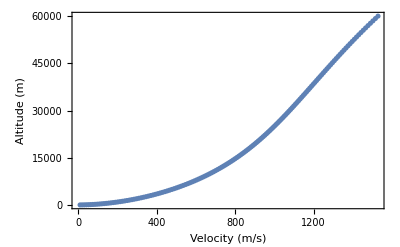

```mathematica
rocketGraph[.5,500,2750000,185000,5,1,9.8]
```

A plot for a single stage rocket without atmospheric drag or gravity

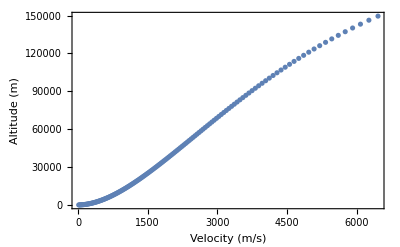

```mathematica
rocketGraph[.5,800,2750000,185000,5,0,0]
```

A plot for a singe stage rocket without atmospheric drag, but with gravity

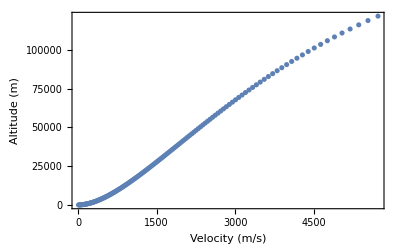

```mathematica
rocketGraph[.5,800,2750000,185000,5,0,9.8]
```

A plot for a single stage rocket with atmospheric drag, but no gravity. Note the lag in velocity as the rocket accelerates and that even though there is no gravity the rocket does not make it much higher than in the standard plot with drag and gravity.

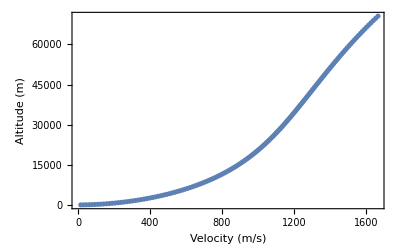

```mathematica
rocketGraph[.5,500,2750000,185000,5,1,0]
```

### Accuracy Testing (Old)

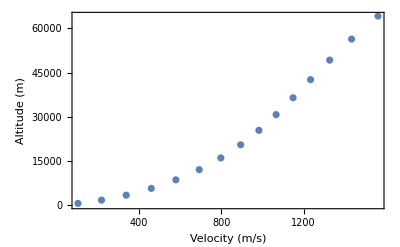

```mathematica
rocketGraph[5,500,2750000,185000,5,1,9.8]
```

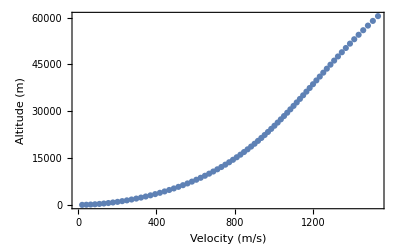

```mathematica
rocketGraph[1,500,2750000,185000,5,1,9.8]
```

```mathematica
rocketGraph[.5,500,2750000,185000,5,1,9.8]
```

-Graphics-

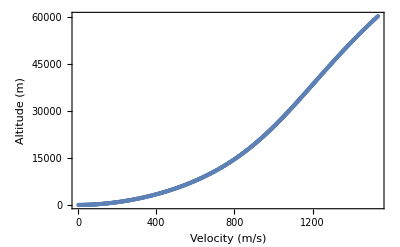

```mathematica
rocketGraph[.1,500,2750000,185000,5,1,9.8]
```

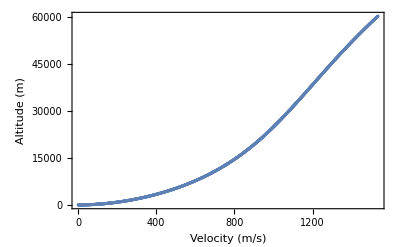

```mathematica
rocketGraph[.05,500,2750000,185000,5,1,9.8]
```

Commented out these calculations so that when you evaluate notebook these cells aren’t run. (They take some time)

```mathematica
(*rocketLive[5,500,2750000,185000,5,1,9.8]
rocketLive[1,500,2750000,185000,5,1,9.8]
rocketLive[.5,500,2750000,185000,5,1,9.8]
rocketLive[.1,500,2750000,185000,5,1,9.8]
rocketLive[.05,500,2750000,185000,5,1,9.8]
rocketLive[.001,500,2750000,185000,5,1,9.8]
rocketLive[.0001,500,2750000,185000,5,1,9.8]*)
```

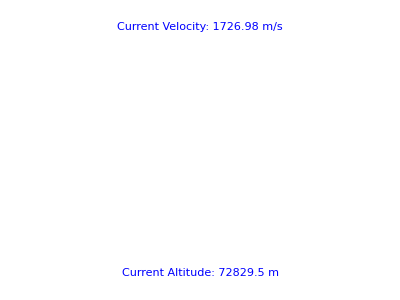

-Graphics-

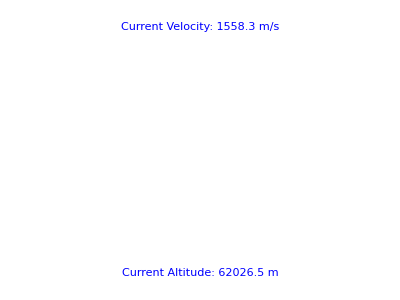

-Graphics-

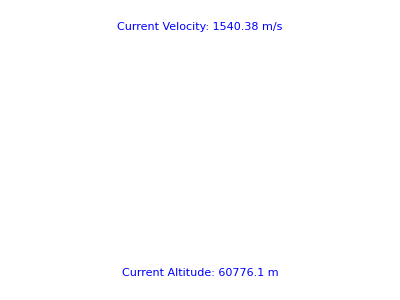

-Graphics-

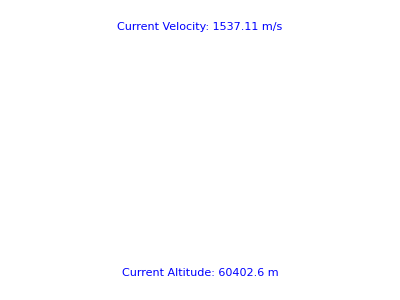

-Graphics-

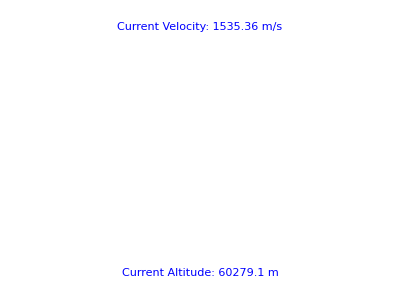

-Graphics-

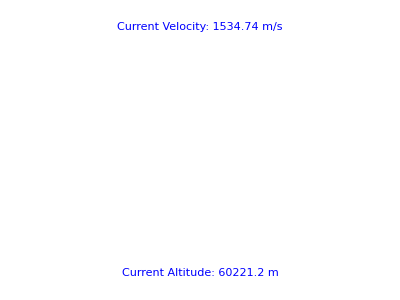

-Graphics-

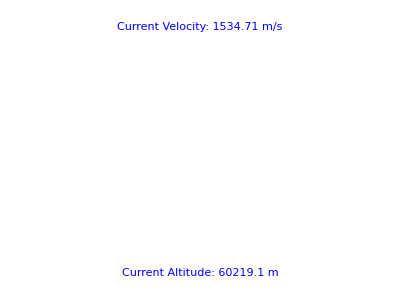

-Graphics-

```mathematica
(*rocketLive[.00001,500,2750000,185000,5,1,9.8]*)
```

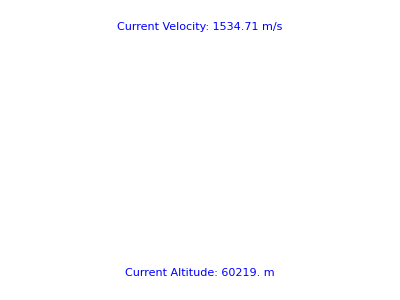

-Graphics-